```mathematica
Clear[p,h,a,z,t,z1,z2]
p[{z1_,z2_}]:= {z2-2ⅈ z1^2+z2^2,ⅈ+2-2 z2-z1+2 z1^2}
γ=Normalize[1+4 ⅈ];
h[z_,t_]:= γ(1-t)p[z]+ t{z⟦1⟧^2-1,z⟦2⟧^2-1}
Dzh[{z1_,z2_},t_]=D[h[{z1,z2},t],{{z1,z2}}];
Dah[{z1_,z2_},t_]=D[h[{z1,z2},t],t];
StartPts=NSolveValues[h[{z1,z2},1]=={0,0},{z1,z2}];
Do[
zSol[i]=NDSolveValue[{
z'[t]==LinearSolve[Dzh[z[t],t],-Dah[z[t],t]],
z[1]==StartPts⟦i⟧},
z,{t,1,0}],
{i,Length[StartPts]}]
HomotopyRoots=Sort[Table[zSol[i][0],{i,Length[StartPts]}]];
MmaRoots=Sort[NSolveValues[p[{z1,z2}]=={0,0},{z1,z2}]];
TableForm[{MmaRoots,HomotopyRoots},TableDirections->Row,TableHeadings->{{"NSolve","Homotopy"},Automatic}]
```

| NSolve | Homotopy
1 | -0.335183+0.764222 ⅈ | 0.695903-0.39442 ⅈ | -0.335183+0.764222 ⅈ | 0.695903-0.39442 ⅈ
2 | -0.141083-1.81579 ⅈ | -2.20665+1.92025 ⅈ | -0.141083-1.81579 ⅈ | -2.20665+1.92025 ⅈ
3 | 0.634012-0.548829 ⅈ | 0.783751+0.0784863 ⅈ | 0.634012-0.548829 ⅈ | 0.783751+0.0784863 ⅈ
4 | 0.842254+1.6004 ⅈ | -1.27301+2.39568 ⅈ | 0.842254+1.6004 ⅈ | -1.27301+2.39568 ⅈ

We can see the paths in ℂ^2.

```mathematica
TabView[Table[
Subscript["z", i]->ParametricPlot[
{ReIm[zSol[1][a]⟦i⟧],ReIm[zSol[2][a]⟦i⟧],ReIm[zSol[3][a]⟦i⟧],ReIm[zSol[4][a]]⟦i⟧},
{a,0,1},PlotRange->All,PlotLegends->Automatic],{i,2}],2]
```

12

You can see the preservation of the target zeros.  Remember they start at 1 and head down to zero.

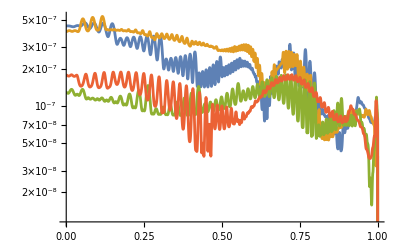

```mathematica
LogPlot[{
Norm[h[zSol[1][t],t]],
Norm[h[zSol[2][t],t]],
Norm[h[zSol[3][t],t]],
Norm[h[zSol[4][t],t]]
},
{t,0, 1}]
```

## Ramification Points

Here are the ramification points of the system.

```mathematica
Clear[h,z,a,z1,z2]
h[z_,a_]:= {z2-2ⅈ z1^2+z2^2,ⅈ+2-2 z2-z1+2 z1^2}+ a{z1^2-1,z2^2-1}
Dzh[{z1_,z2_},a_]=D[h[{z1,z2},a],{{z1,z2}}];
z1z2aRamPts=NSolveValues[{h[{z1,z2},a]=={0,0},Det[Dzh[{z1,z2},a]]==0},{z1,z2,a}];
TableForm[z1z2aRamPts,TableHeadings->{Automatic,{"z_1","z_2","a"}}]
```

| z_1 | z_2 | a
1 | 2.72707+4.24798 ⅈ | -1.65138-6.13974 ⅈ | -1.05179+0.946396 ⅈ
2 | -1.00771-0.227426 ⅈ | 0.228828-0.125659 ⅈ | 4.77892+2.20113 ⅈ
3 | -0.980414+0.689285 ⅈ | 1.43257+0.883344 ⅈ | 1.57894+0.599339 ⅈ
4 | 0.024628-0.0981652 ⅈ | 1.17046-0.227325 ⅈ | 2.45331-0.746536 ⅈ
5 | 0.0972649-1.61341 ⅈ | -0.845393+0.640239 ⅈ | -0.208202+1.33858 ⅈ
6 | 1.09845+0.390764 ⅈ | 0.252116-0.287908 ⅈ | 2.80614+2.44731 ⅈ
7 | 0.172233-0.165754 ⅈ | -1.28222-1.08285 ⅈ | -0.827305+1.74072 ⅈ
8 | 0.0555323-0.00872266 ⅈ | -1.40365+0.96381 ⅈ | -0.367087-1.75282 ⅈ
9 | 1.20879-0.162409 ⅈ | 0.880076+1.16973 ⅈ | 1.04282+0.11592 ⅈ
10 | 0.461391+1.67472 ⅈ | -0.957056+0.717873 ⅈ | 0.137762+1.31975 ⅈ
11 | 0.182885+0.172559 ⅈ | 0.497744+0.310265 ⅈ | 0.736464+0.660698 ⅈ
12 | 1.18142-3.38783 ⅈ | 1.97183-3.29541 ⅈ | -1.07997+1.12952 ⅈ

If I pick γ=1/a I should hit a ramification point at t=1/2 for at least some of the paths. With default settings I lose a path if I do this with the first ramification point.

```mathematica
Clear[p,h,a,z,t,z1,z2]
{z1R,z2R,a}=z1z2aRamPts⟦1⟧;
p[{z1_,z2_}]:= {z2-2ⅈ z1^2+z2^2,ⅈ+2-2 z2-z1+2 z1^2}
γ=0.000000001+1/a;
h[z_,t_]:= γ(1-t)p[z]+ t{z⟦1⟧^2-1,z⟦2⟧^2-1}
Dzh[{z1_,z2_},t_]=D[h[{z1,z2},t],{{z1,z2}}];
Dah[{z1_,z2_},t_]=D[h[{z1,z2},t],t];
StartPts=NSolveValues[h[{z1,z2},1]=={0,0},{z1,z2}];
Do[
zSol[i]=NDSolveValue[{
z'[t]==LinearSolve[Dzh[z[t],t],-Dah[z[t],t]],
z[1]==StartPts⟦i⟧},
z,{t,1,0}],
{i,Length[StartPts]}]
TabView[Table[
Subscript["z", i]->ParametricPlot[
{ReIm[zSol[1][a]⟦i⟧],ReIm[zSol[2][a]⟦i⟧],ReIm[zSol[3][a]⟦i⟧],ReIm[zSol[4][a]]⟦i⟧},
{a,0,1},Epilog->{Red, Point[ReIm[z1R]],Point[ReIm[z2R]]},
PlotPoints->100,PlotRange->20{{-1,1},{-1,1}},PlotLegends->Automatic],{i,2}],2]
```

12

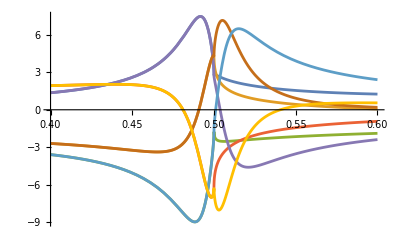

```mathematica
Plot[ {
Re[zSol[2][t]⟦1⟧],
Im[zSol[2][t]⟦1⟧],
Re[zSol[2][t]⟦2⟧],
Im[zSol[2][t]⟦2⟧],
Re[zSol[3][t]⟦1⟧],
Im[zSol[3][t]⟦1⟧],
Re[zSol[3][t]⟦2⟧],
Im[zSol[3][t]⟦2⟧]
},{t,0.4, 0.6}]
```

```mathematica
Clear[z1,z2,a]
Table[
{z1,z2,a}=z1z2aRamPts⟦i⟧;
{a,SingularValueList[ Dzh[{z1,z2},a],Tolerance->0]},
{i,1, Length[z1z2aRamPts]}]
```

{{-1.05179+0.946396 ⅈ,{32.1904,1.43138×10^-13}},{4.77892+2.20113 ⅈ,{11.2505,3.49201×10^-16}},{1.57894+0.599339 ⅈ,{9.89626,5.20965×10^-15}},{2.45331-0.746536 ⅈ,{5.71594,3.24039×10^-15}},{-0.208202+1.33858 ⅈ,{8.17726,7.73442×10^-15}},{2.80614+2.44731 ⅈ,{7.82829,6.92975×10^-14}},{-0.827305+1.74072 ⅈ,{5.4891,6.8677×10^-15}},{-0.367087-1.75282 ⅈ,{5.59669,1.15978×10^-15}},{1.04282+0.11592 ⅈ,{7.93681,2.35315×10^-14}},{0.137762+1.31975 ⅈ,{8.77587,1.60158×10^-14}},{0.736464+0.660698 ⅈ,{3.09204,3.48277×10^-15}},{-1.07997+1.12952 ⅈ,{22.3562,1.63853×10^-13}}}

```mathematica
a
```

-0.47637